# David Meretzky 785 Homework 2 FEM

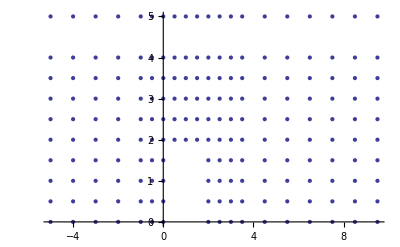

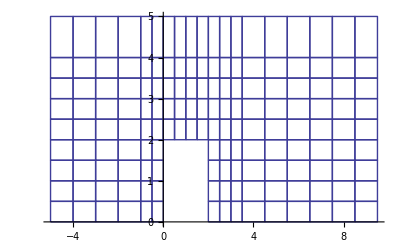

((-x+γ) (-y+δ))/((-α+γ) (-β+δ))

((x-α) (-y+δ))/((-α+γ) (-β+δ))

((x-α) (y-β))/((-α+γ) (-β+δ))

((y-β) (-x+γ))/((-α+γ) (-β+δ))

```mathematica
nodes = Import["/Users/David/Downloads/ChnlNodes.dat"];
elements = Import["/Users/David/Downloads/ChnlElems.dat"];

el= {};
For[i = 1, i ≤  155, i++,
node = nodes[[elements[[i,2;;5]],2;;3]];
 AppendTo[node,nodes[[elements[[i,2;;5]],2;;3]][[1]]];
AppendTo[el,node];
];

ListPlot[nodes[[1;;188,2;;3]]]
ListLinePlot[el, PlotStyle->Hue[.67, .6, .6]]

n1[α_,β_,γ_,δ_,x_,y_] = (((γ - x)*(δ - y))/((γ - α)*(δ-β)));
n2[α_,β_,γ_,δ_,x_,y_] = (((x - α)*(δ - y))/((γ - α)*(δ-β)));
n3[α_,β_,γ_,δ_,x_,y_] = (((x - α)*(y - β))/((γ - α)*(δ-β)));n4[α_,β_,γ_,δ_,x_,y_] = (((γ - x)*(y - β))/((γ - α)*(δ-β)));


Print[n1[α,β,γ,δ,x,y]];
Print[n2[α,β,γ,δ,x,y]];
Print[n3[α,β,γ,δ,x,y]];
Print[n4[α,β,γ,δ,x,y]];

(*For[i = 1, i ≤ 155, ++i, 
element = elements[[i]];
α = nodes[[element[[2;;5]]]][[1]][[2]];
β = nodes[[element[[2;;5]]]][[1]][[3]];
γ = nodes[[element[[2;;5]]]][[3]][[1]];
δ = nodes[[element[[2;;5]]]][[3]][[2]];
Print[n1[α,β,γ,δ,x,y]];
Print[n2[α,β,γ,δ,x,y]];
Print[n3[α,β,γ,δ,x,y]];
Print[n4[α,β,γ,δ,x,y]];
];*)
```

```mathematica
locals = {};
For[i = 1, i ≤ 155, ++i, 

Print[i];
element = elements[[i]];
α = nodes[[element[[2;;5]]]][[1]][[2]];
β = nodes[[element[[2;;5]]]][[1]][[3]];
γ = nodes[[element[[2;;5]]]][[3]][[2]];
δ = nodes[[element[[2;;5]]]][[3]][[3]];
(*Print[n1[α,β,γ,δ,x,y]];
Print[n2[α,β,γ,δ,x,y]];
Print[n3[α,β,γ,δ,x,y]];
Print[n4[α,β,γ,δ,x,y]];*)

polynomials = {n1[α,β,γ,δ,x,y],n2[α,β,γ,δ,x,y],n3[α,β,γ,δ,x,y],n4[α,β,γ,δ,x,y]};

local = ConstantArray[0,{4,4}];

For[j = 1,j ≤ 4, j++, 

js =  {D[polynomials[[j]],x],
D[polynomials[[j]],y]};
For[k =1, k ≤ 4, k ++, 

ks = {D[polynomials[[k]],x],
D[polynomials[[k]],y]};
product =js.ks;
(* To be replaced with Gaussian Quadrature...  *)

local[[j,k]] =∫_β^δ ∫_α^γ productⅆxⅆy;
];
];
AppendTo[locals, local];
];
```

```mathematica
re2 = Range[188]-Range[188];

For[i = 1, i ≤155, i++, 
element = elements[[i]];
α = nodes[[element[[2;;5]]]][[1]][[2]];
β = nodes[[element[[2;;5]]]][[1]][[3]];
γ = nodes[[element[[2;;5]]]][[3]][[2]];
δ = nodes[[element[[2;;5]]]][[3]][[3]];

polynomials = {n1[α,β,γ,δ,x,y],n2[α,β,γ,δ,x,y],n3[α,β,γ,δ,x,y],n4[α,β,γ,δ,x,y]};


If[i ≤ 9, 


re2[[element[[5]]]]-=∫_β^δ (polynomials[[4]]/.x->α) ⅆy;

re2[[element[[2]]]]-=∫_β^δ (polynomials[[1]]/.x->α) ⅆy;
];

If[i ≥ 147, 

re2[[element[[4]]]]+=∫_β^δ (polynomials[[3]]/.x->γ)ⅆy;

re2[[element[[3]]]]+=∫_β^δ (polynomials[[2]]/.x->γ)ⅆy;
];
];
```